```mathematica
whichEquils=Range[Dimensions[Jeq][[1]]];
```

```mathematica
equilP= equil/.c0aPΝparsH;
Jeq=J/.c0aPΝparsH/.equilP//Simplify;
```

```mathematica
Eigs = Map[Eigenvalues,Jeq[[whichEquils]]];
domEigs= Map[Max,Map[Re,Eigs]];
equilP=equilP[[whichEquils]];
```

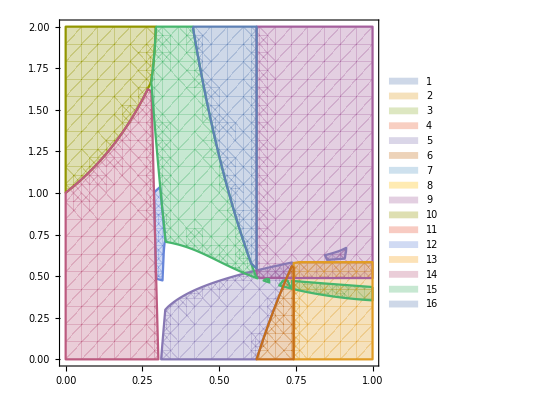

```mathematica
RegPlot = RegionPlot[
Evaluate@Thread[domEigs<0],
{c0,0,1},{aPΝ,0,2},
PlotLegends->whichEquils]
```

```mathematica
All3Pos[x_]:=AllTrue[x[[1;;3,2]],Positive]
```

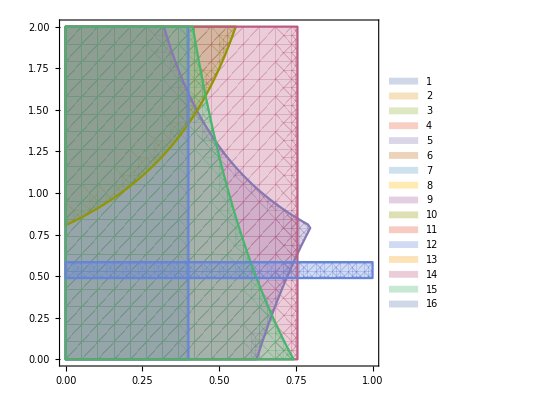

```mathematica
RegPlot = RegionPlot[
Evaluate@Map[All3Pos,equil[[whichEquils]]/.c0aPΝparsH],
{c0,0,1},{aPΝ,0,2},
PlotLegends->whichEquils]
```

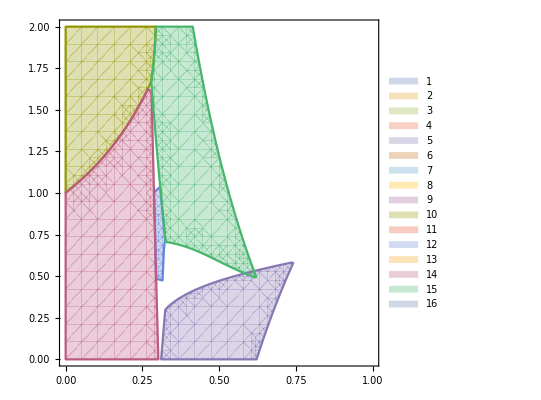

```mathematica
RegPlot3sp = RegionPlot[
Evaluate@Thread[
Evaluate@Thread[domEigs<0]
&&
Evaluate@Map[All3Pos,equilP]
],
{c0,0,1},{aPΝ,0,2},
PlotLegends->whichEquils]
```

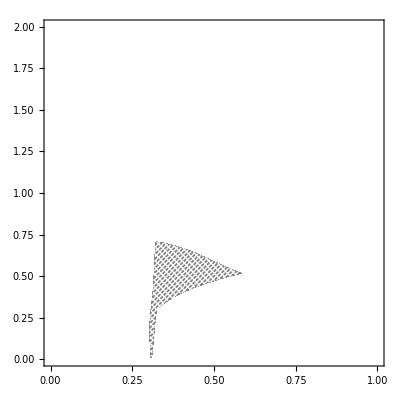

```mathematica
RegPlot3sp = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{c0,0,1},{aPΝ,0,2},
Mesh->25,MeshFunctions->{2#1+#2&,2#1-#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->10,
BoundaryStyle->None,
PlotRange->{{0,1},{0,2}}]
```